# Embedded Pathways

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/trvrb/Documents/src/embedded-pathways/analysis

## Data

### Ordination

```mathematica
ordinationData=Import["../results/ordination.tsv"];
```

```mathematica
headings=ordinationData[[1]]
```

{id,umap_1,umap_2,tsne_1,tsne_2,pca_1,pca_2}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,headings]
```

{id→1,umap_1→2,umap_2→3,tsne_1→4,tsne_2→5,pca_1→6,pca_2→7}

```mathematica
ordinationData=Drop[ordinationData,1];
```

```mathematica
nodes=Union[ordinationData[[All,1]]];
```

```mathematica
toUmap1=Map[#[[1]]->#[[2]]&,ordinationData[[All,{1,2}]]];
```

```mathematica
toUmap2=Map[#[[1]]->#[[2]]&,ordinationData[[All,{1,3}]]];
```

```mathematica
toTsne1=Map[#[[1]]->#[[2]]&,ordinationData[[All,{1,4}]]];
```

```mathematica
toTsne2=Map[#[[1]]->#[[2]]&,ordinationData[[All,{1,5}]]];
```

```mathematica
toPca1=Map[#[[1]]->#[[2]]&,ordinationData[[All,{1,6}]]];
```

```mathematica
toPca2=Map[#[[1]]->#[[2]]&,ordinationData[[All,{1,7}]]];
```

### Metadata

```mathematica
metadata=Import["../data/metadata.tsv"];
```

```mathematica
headings=metadata[[1]]
```

{name,parent,clade,S1_mutations}

```mathematica
metadata=Drop[metadata,1];
```

```mathematica
toParent=Map[#[[1]]->#[[2]]&,metadata[[All,{1,2}]]];
```

```mathematica
toClade=Map[#[[1]]->If[StringQ[#[[2]]],StringSplit[#[[2]]," "][[1]],"other"]&,metadata[[All,{1,3}]]];
```

```mathematica
clades=Union[toClade[[All,2]]]
```

{19A,19B,20A,20B,20C,20D,20E,20G,20H,20I,20J,21A,21B,21C,21D,21E,21F,21G,21H,21I,21J,21K,21L,21M,22A,22B,22C,22D,22E,22F,23A,23B,23C,23D,23E,23F,23G,23H,23I,24A,24B,24C,24D,24E,24F,24G,24H,24I,other}

### Embeddings

```mathematica
embeddingsData=Import["../results/embeddings.tsv"];
```

```mathematica
headings=embeddingsData[[1,1;;10]]
```

{NODE_0000002,0.094207,-0.101992,0.0234941,0.107701,-0.197655,0.0262338,0.229231,-0.173882,-0.263272}

```mathematica
toEmbedding=Map[#[[1]]->#[[2;;-1]]&,embeddingsData];
```

## Clade colors

Download with “nextstrain remote download https://nextstrain.org/ncov/gisaid/reference”

```mathematica
treeJson=Import["../data/ncov_gisaid_reference.json","RawJSON"];
```

```mathematica
metaColorMapping=Map[StringSplit[#[[1]]," "][[1]]->RGBColor[#[[2]]]&,FirstCase[treeJson["meta"]["colorings"],x_/;x["key"]=="clade_membership"]["scale"]]
```

{20H→RGBColor[0.3686274509803922, 0.11372549019607843, 0.615686274509804],20I→RGBColor[0.30980392156862746, 0.12156862745098039, 0.6666666666666666],20J→RGBColor[0.28627450980392155, 0.16470588235294117, 0.7098039215686275],21A→RGBColor[0.2627450980392157, 0.20392156862745098, 0.7490196078431373],21I→RGBColor[0.25098039215686274, 0.25098039215686274, 0.7803921568627451],21J→RGBColor[0.24705882352941178, 0.3058823529411765, 0.796078431372549],21B→RGBColor[0.24313725490196078, 0.3568627450980392, 0.8156862745098039],21C→RGBColor[0.25098039215686274, 0.40784313725490196, 0.8117647058823529],21D→RGBColor[0.2627450980392157, 0.4549019607843137, 0.803921568627451],21E→RGBColor[0.27058823529411763, 0.5019607843137255, 0.792156862745098],21F→RGBColor[0.28627450980392155, 0.5411764705882353, 0.7686274509803922],21G→RGBColor[0.30196078431372547, 0.5764705882352941, 0.7450980392156863],21H→RGBColor[0.3215686274509804, 0.6078431372549019, 0.7098039215686275],21K→RGBColor[0.34509803921568627, 0.6352941176470588, 0.6745098039215687],21L→RGBColor[0.3686274509803922, 0.6588235294117647, 0.6352941176470588],21M→RGBColor[0.396078431372549, 0.6784313725490196, 0.596078431372549],22A→RGBColor[0.4196078431372549, 0.6980392156862745, 0.5529411764705883],22B→RGBColor[0.45098039215686275, 0.7098039215686275, 0.5137254901960784],22C→RGBColor[0.48627450980392156, 0.7215686274509804, 0.4745098039215686],22D→RGBColor[0.5176470588235295, 0.7294117647058823, 0.43529411764705883],22E→RGBColor[0.5529411764705883, 0.7372549019607844, 0.403921568627451],22F→RGBColor[0.592156862745098, 0.7411764705882353, 0.37254901960784315],23A→RGBColor[0.6274509803921569, 0.7450980392156863, 0.34509803921568627],23B→RGBColor[0.6666666666666666, 0.7411764705882353, 0.3215686274509804],23C→RGBColor[0.7058823529411765, 0.7411764705882353, 0.2980392156862745],23D→RGBColor[0.7411764705882353, 0.7333333333333333, 0.28627450980392155],23E→RGBColor[0.7725490196078432, 0.7254901960784313, 0.27058823529411763],23F→RGBColor[0.803921568627451, 0.7137254901960784, 0.25882352941176473],23G→RGBColor[0.8313725490196079, 0.6941176470588235, 0.24705882352941178],23H→RGBColor[0.8588235294117647, 0.6745098039215687, 0.23921568627450981],23I→RGBColor[0.8745098039215686, 0.6431372549019608, 0.23137254901960785],24A→RGBColor[0.8901960784313725, 0.6078431372549019, 0.2235294117647059],24B→RGBColor[0.9019607843137255, 0.5686274509803921, 0.21568627450980393],24C→RGBColor[0.9019607843137255, 0.5176470588235295, 0.20392156862745098],24D→RGBColor[0.9019607843137255, 0.4666666666666667, 0.19607843137254902],24E→RGBColor[0.8941176470588236, 0.40784313725490196, 0.1843137254901961],24F→RGBColor[0.8862745098039215, 0.34509803921568627, 0.17254901960784313],24G→RGBColor[0.8784313725490196, 0.2823529411764706, 0.1568627450980392],24H→RGBColor[0.8705882352941177, 0.2196078431372549, 0.14901960784313725],24I→RGBColor[0.8588235294117647, 0.1568627450980392, 0.13725490196078433]}

Non-variant clades need to be assigned grays

```mathematica
earlyColorMapping=MapThread[#1->#2&,{{"19A","19B","20A","20B","20C","20D","20E","20F","20G","21F","other"},Table[GrayLevel[x],{x,0.25,0.75,0.5/10}]}]
```

{19A→GrayLevel[0.25],19B→GrayLevel[0.3],20A→GrayLevel[0.35],20B→GrayLevel[0.4],20C→GrayLevel[0.45],20D→GrayLevel[0.5],20E→GrayLevel[0.55],20F→GrayLevel[0.6000000000000001],20G→GrayLevel[0.65],21F→GrayLevel[0.7],other→GrayLevel[0.75]}

```mathematica
cladeToColor=Join[earlyColorMapping,metaColorMapping]
```

{19A→GrayLevel[0.25],19B→GrayLevel[0.3],20A→GrayLevel[0.35],20B→GrayLevel[0.4],20C→GrayLevel[0.45],20D→GrayLevel[0.5],20E→GrayLevel[0.55],20F→GrayLevel[0.6000000000000001],20G→GrayLevel[0.65],21F→GrayLevel[0.7],other→GrayLevel[0.75],20H→RGBColor[0.3686274509803922, 0.11372549019607843, 0.615686274509804],20I→RGBColor[0.30980392156862746, 0.12156862745098039, 0.6666666666666666],20J→RGBColor[0.28627450980392155, 0.16470588235294117, 0.7098039215686275],21A→RGBColor[0.2627450980392157, 0.20392156862745098, 0.7490196078431373],21I→RGBColor[0.25098039215686274, 0.25098039215686274, 0.7803921568627451],21J→RGBColor[0.24705882352941178, 0.3058823529411765, 0.796078431372549],21B→RGBColor[0.24313725490196078, 0.3568627450980392, 0.8156862745098039],21C→RGBColor[0.25098039215686274, 0.40784313725490196, 0.8117647058823529],21D→RGBColor[0.2627450980392157, 0.4549019607843137, 0.803921568627451],21E→RGBColor[0.27058823529411763, 0.5019607843137255, 0.792156862745098],21F→RGBColor[0.28627450980392155, 0.5411764705882353, 0.7686274509803922],21G→RGBColor[0.30196078431372547, 0.5764705882352941, 0.7450980392156863],21H→RGBColor[0.3215686274509804, 0.6078431372549019, 0.7098039215686275],21K→RGBColor[0.34509803921568627, 0.6352941176470588, 0.6745098039215687],21L→RGBColor[0.3686274509803922, 0.6588235294117647, 0.6352941176470588],21M→RGBColor[0.396078431372549, 0.6784313725490196, 0.596078431372549],22A→RGBColor[0.4196078431372549, 0.6980392156862745, 0.5529411764705883],22B→RGBColor[0.45098039215686275, 0.7098039215686275, 0.5137254901960784],22C→RGBColor[0.48627450980392156, 0.7215686274509804, 0.4745098039215686],22D→RGBColor[0.5176470588235295, 0.7294117647058823, 0.43529411764705883],22E→RGBColor[0.5529411764705883, 0.7372549019607844, 0.403921568627451],22F→RGBColor[0.592156862745098, 0.7411764705882353, 0.37254901960784315],23A→RGBColor[0.6274509803921569, 0.7450980392156863, 0.34509803921568627],23B→RGBColor[0.6666666666666666, 0.7411764705882353, 0.3215686274509804],23C→RGBColor[0.7058823529411765, 0.7411764705882353, 0.2980392156862745],23D→RGBColor[0.7411764705882353, 0.7333333333333333, 0.28627450980392155],23E→RGBColor[0.7725490196078432, 0.7254901960784313, 0.27058823529411763],23F→RGBColor[0.803921568627451, 0.7137254901960784, 0.25882352941176473],23G→RGBColor[0.8313725490196079, 0.6941176470588235, 0.24705882352941178],23H→RGBColor[0.8588235294117647, 0.6745098039215687, 0.23921568627450981],23I→RGBColor[0.8745098039215686, 0.6431372549019608, 0.23137254901960785],24A→RGBColor[0.8901960784313725, 0.6078431372549019, 0.2235294117647059],24B→RGBColor[0.9019607843137255, 0.5686274509803921, 0.21568627450980393],24C→RGBColor[0.9019607843137255, 0.5176470588235295, 0.20392156862745098],24D→RGBColor[0.9019607843137255, 0.4666666666666667, 0.19607843137254902],24E→RGBColor[0.8941176470588236, 0.40784313725490196, 0.1843137254901961],24F→RGBColor[0.8862745098039215, 0.34509803921568627, 0.17254901960784313],24G→RGBColor[0.8784313725490196, 0.2823529411764706, 0.1568627450980392],24H→RGBColor[0.8705882352941177, 0.2196078431372549, 0.14901960784313725],24I→RGBColor[0.8588235294117647, 0.1568627450980392, 0.13725490196078433]}

```mathematica
variantLegend=SwatchLegend[Table[clade/.cladeToColor,{clade,clades}],Table[clade,{clade,clades}],LegendLayout->{"Row",1}];
```

```mathematica
smallVariantLegend=SwatchLegend[Table[clade/.cladeToColor,{clade,clades}],Table[clade,{clade,clades}],LegendLayout->{"Column",1},LabelStyle->{FontSize->10}];
```

## Ordinations

```mathematica
figFromOrdinationRules[dimen1_,dimen2_,name_]:=Module[{points,lines,colors,pointFig,lineFig},
points=Table[Tooltip[{node/.dimen1,node/.dimen2},node],{node,nodes}];
lines=Table[With[{parent=node/.toParent},{{node/.dimen1,node/.dimen2},{parent/.dimen1,parent/.dimen2}}],{node,nodes}];
colors=Table[node/.toClade/.cladeToColor,{node,nodes}];
pointFig=ListPlot[Map[{#}&,points],PlotTheme->"FulLAxes",PlotRange->All,ImageSize->500,Frame->{True,True,False,False},FrameLabel->{name<>" dimen 1",name<>" dimen 2"},Axes->False,PlotStyle->colors];
lineFig=ListLinePlot[lines,PlotTheme->"FulLAxes",PlotRange->All,ImageSize->600,Frame->{True,True,False,False},FrameLabel->{name<>" dimen 1",name<>" dimen 2"},Axes->False,PlotStyle->Directive[Opacity[0.25],GrayLevel[0.25]]];
Show[lineFig,pointFig]
]
```

```mathematica
umapFig=figFromOrdinationRules[toUmap1,toUmap2,"UMAP"];
```

```mathematica
Export["figures/umap.png",umapFig,"PNG",ImageResolution->300]
```

figures/umap.png

```mathematica
tsneFig=figFromOrdinationRules[toTsne1,toTsne2,"t-SNE"];
```

```mathematica
Export["figures/tsne.png",tsneFig,"PNG",ImageResolution->300]
```

figures/tsne.png

```mathematica
pcaFig=figFromOrdinationRules[toPca1,toPca2,"PCA"];
```

```mathematica
Export["figures/pca.png",pcaFig,"PNG",ImageResolution->300]
```

figures/pca.png

## Direct embeddings

```mathematica
embeddingStandardDeviations=Map[StandardDeviation,Transpose[Table[node/.toEmbedding,{node,nodes}]]];
```

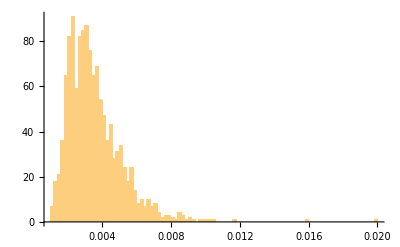

```mathematica
Histogram[embeddingStandardDeviations,100,PlotRange->All]
```

```mathematica
pos=Position[embeddingStandardDeviations,x_/;x>0.01]
```

{{188},{235},{569},{727},{877},{1161}}

```mathematica
Reverse[Ordering[embeddingStandardDeviations]][[1;;5]]
```

{1161,877,727,188,235}

```mathematica
extractEmbedding[dimen_]:=Map[#[[1]]->#[[2,dimen]]&,toEmbedding]
```

```mathematica
figFromOrdinationRules[extractEmbedding[1161],extractEmbedding[877],"Embedding"];
```

```mathematica
figFromOrdinationRules[extractEmbedding[727],extractEmbedding[188],"Embedding"];
```